```mathematica
SetDirectory[NotebookDirectory[]]
pblue=Lighter[Blue];
pyellow=Lighter[Yellow];
pred=Lighter[Red];
pgreen=Lighter[Green];
cf=Piecewise[{{Blend[{pred,pblue},(#+Pi)/(Pi/2)],#≤-Pi/2},{Blend[{pblue,pgreen},(#+Pi/2)/(Pi/2)],#≤0},{Blend[{pgreen,pyellow},(#)/(Pi/2)],#≤Pi/2},{Blend[{pyellow,pred},(#-Pi/2)/(Pi/2)],#≤Pi}}]&;
rasterizeBackground[g_,res_: 100]:=Show[Graphics[{Inset[Rasterize[Show[g,ImagePadding->0,ImageMargins->0,LabelStyle->Opacity[0],FrameTicksStyle->Opacity[0],FrameStyle->Opacity[0],AxesStyle->Opacity[0],TicksStyle->Opacity[0],PlotRangeClipping->False],ImageResolution->res],Scaled[{0,0}],Scaled[{0,0}],Scaled[1]]}],Sequence@@Options[g],Sequence@@Options[g,PlotRange],Sequence@@Options[g,Epilog]]
phase[l:{_?NumericQ..}]:=Module[{args=Arg[l]},args+Prepend[2Pi Accumulate@-IntegerPart@Differences[args/Pi],0]]
nmax=10;
getphase[sig_]:=Module[{asig,plst,S1,slst1,f1},
asig=Fourier[ReplacePart[InverseFourier[sig-Mean[sig]],Join[{{1}},{#}&/@(Floor[Length[sig]/2]+Range[Floor[Length[sig]/2]])]->0]];
plst=phase[asig];
S1[n_]:=Sum[Exp[-I*n*plst[[i]]], {i,1,Length[plst]}]/Length[plst];
slst1=Table[S1[n]/(I*n),{n,1,nmax}];
f1[θ_]:=θ+Evaluate[Sum[2*Re[slst1][[n]]*(Cos[n*θ]-1)-2*Im[slst1][[n]]*Sin[n*θ],{n,1,nmax}]];
f1/@plst]
```

/Users/zack/Documents/oscillators/snakingoscillators

#### Single trajectory runs

-Graphics-

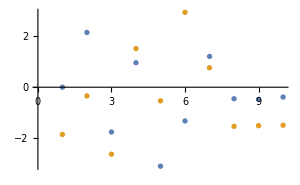
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
filebase="data/chimeras/2";
dat=BinaryReadList[filebase<>"phases.npy","Real64"][[17;;-1]];
{seed,order,period,norm}=Import[filebase<>"out.dat"][[-1]];
M=10;
theta=ArcTan[Partition[dat,4*M][[All,1;;M]],Partition[dat,4*M][[All,M+1;;2*M]]];
phi=ArcTan[Partition[dat,4*M][[All,2*M+1;;3*M]],Partition[dat,4*M][[All,3*M+1;;4*M]]];
orders=BinaryReadList[filebase<>"order.npy","Real64"][[17;;-1]];
rasterizeBackground[ListPlot[orders,ImageSize->300]]
phases=Transpose[Catenate[{Transpose[theta],Transpose[phi]}]];
dphases=(Mod[#-#[[1]]+Pi,2*Pi]-Pi&/@phases);

If[period>0,
nperiod=Round[period/0.1];
Grid[{{rasterizeBackground[ListDensityPlot[dphases[[1;;nperiod,1;;M]],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]],rasterizeBackground[ListDensityPlot[dphases[[1;;nperiod,M+1;;2*M]],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]],rasterizeBackground[ListPlot[Transpose[{Cos[dphases[[All,2]]],Cos[dphases[[All,M+1]]]}],PlotRange->{{-1,1},{-1,1}},ImageSize->300]],ListPlot[{dphases[[-1,1;;M]],dphases[[-1,M+1;;-1]]},ImageSize->300]}}]]
If[Length[periods]>0,{period,Mean[orders[[-period;;-1]]],Norm[Differences[dphases[[-period+1;;-1]]],2]}]
```

```mathematica
Mean[Table[Abs[Sum[1/(2*M)*(Exp[I*theta[[n,i]]]+Exp[I*phi[[n,i]]]),{i,1,M}]]^2,{n,1,nperiod}]]^0.5
Mean[Table[Abs[Sum[1/(2*M)*(Exp[I*(theta[[n,i]]+2*Pi/M*(i-1))]+Exp[I*(phi[[n,i]]+2*Pi/M*(i-1))]),{i,1,M}]]^2,{n,1,nperiod}]]^0.5
Mean[Table[Abs[Sum[1/(2*M)*(Exp[I*(theta[[n,i]]-2*Pi/M*(i-1))]+Exp[I*(phi[[n,i]]-2*Pi/M*(i-1))]),{i,1,M}]]^2,{n,1,nperiod}]]^0.5
```

0.309501

0.276878

0.219421

#### Chimeras from random initial conditions

```mathematica
vals={#[[1]],#[[2]],#[[3]]/300,#[[4]]}&/@SortBy[Import["random.dat"],Norm[#[[2;;4]]]&];
dorder=0.01;
dperiod=0.01;
dnorm=0.01;
{bins,array}=HistogramList[vals[[All,2;;4]],{{dorder*(Range[1/dorder]-1)},{0.1+dperiod*(Range[3/dperiod]-1)},{dnorm*(Range[2/dnorm]-1)}}];
uniq=Table[{i,j,k}=case;
First@Cases[vals,u_/;u[[2]]>=bins[[1,i]]&&u[[2]]<=bins[[1,i+1]]&&u[[3]]>=bins[[2,j]]&&u[[3]]<=bins[[2,j+1]]&&u[[4]]>=bins[[3,k]]&&u[[4]]<=bins[[3,k+1]]],{case,(First/@ArrayRules[array])[[1;;-2]]}];
Length[uniq]
SortBy[{#[[1]],#[[2]],#[[3]]*300,#[[4]]}&/@uniq,{#[[2]],#[[3]],#[[4]]}&]

If[!DirectoryQ["data/chimeras"],CreateDirectory["data/chimeras"]]
seeds=uniq[[All,1]];
Do[CopyFile["data/random/"<>ToString[seeds[[i]]]<>"fs.npy","data/chimeras/"<>ToString[i]<>"ic.npy",OverwriteTarget->True], {i,1,Length[seeds]}]
Last/@ArrayRules[array][[1;;-2]]
```

10

{{822,7.86954×10^-16,43.7141,0.237467},{199,0.309889,93.0462,1.62203},{88,0.444722,92.9085,1.10769},{441,0.505823,93.3858,0.480243},{28,0.505863,93.3858,0.479485},{326,0.53729,90.2009,0.273056},{417,0.540555,88.9955,0.275255},{567,0.57116,93.9305,0.164956},{70,0.579997,92.9358,0.597037},{361,0.717616,93.9533,0.0818283}}

{1,1,18,2,1,2,3,63,1,211}

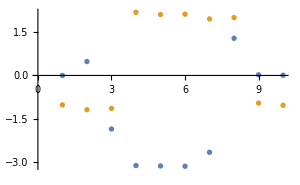
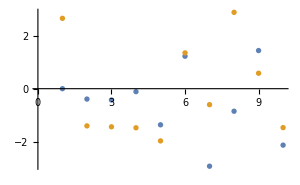
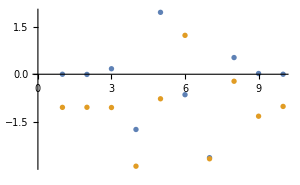
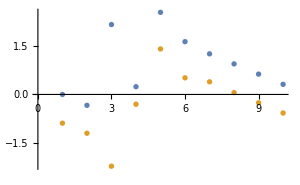
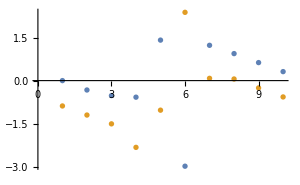
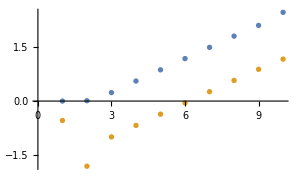
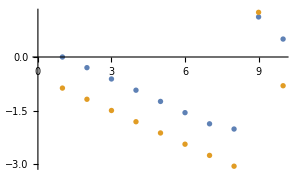
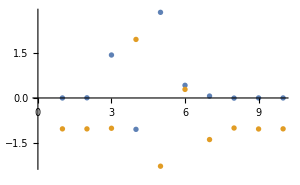
1 | 4.2307×10^-16 | 43.7142 | 0.238113 | 2.42587 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
2 | 0.309914 | 93.0462 | 1.62156 | 24.8733 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
3 | 0.444715 | 92.9096 | 1.10854 | 3.89638 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
4 | 0.505831 | 93.3865 | 0.480094 | 4.12425 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
5 | 0.505873 | 93.3865 | 0.479502 | 3.98015 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
6 | 0.53729 | 90.2019 | 0.27434 | 0.218262 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
7 | 0.540619 | 88.9964 | 0.275104 | 0.689971 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
8 | 0.579997 | 92.9365 | 0.597456 | 12.4475 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
9 | 0.571151 | 93.9308 | 0.165257 | 10.318 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
10 | 0.717596 | 93.9538 | 0.0822271 | 10.9378 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Monitor[p=Grid[DeleteCases[Table[filebase="data/chimeras/"<>ToString[j];
{seed,order,period,norm}=Import[filebase<>"out.dat"][[-1]];
dat=BinaryReadList[filebase<>"phases.npy","Real64"][[17;;-1]];
M=10;
theta=ArcTan[Partition[dat,4*M][[All,1;;M]],Partition[dat,4*M][[All,M+1;;2*M]]];
phi=ArcTan[Partition[dat,4*M][[All,2*M+1;;3*M]],Partition[dat,4*M][[All,3*M+1;;4*M]]];
phases=Transpose[Catenate[{Transpose[theta],Transpose[phi]}]];
phases2=Transpose[Catenate[{-Reverse[Transpose[phi]],-Reverse[Transpose[theta]]}]];
dphases=(Mod[#-#[[1]]+Pi,2*Pi]-Pi&/@phases);
dphases2=(#-#[[1]]&/@phases2);
norms=Norm[Mod[#-dphases[[-1]]+Pi,2*Pi]-Pi]&/@dphases;
mins=First/@Position[Differences[Sign[Differences[norms]]],u_/;u>0];
periods=Differences[Cases[mins,u_/;norms[[u]]<1]];
test=Norm[Mod[dphases[[-Round[period/0.1];;-1]]-dphases[[-10*Round[period/0.1];;-9*Round[period/0.1]-1]]+Pi,2*Pi]-Pi];
If[period>0,
{Grid[{{j,order,period,norm,test,rasterizeBackground[ListDensityPlot[dphases[[1;;Round[period/0.1];;10,1;;M]],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]],rasterizeBackground[ListDensityPlot[dphases[[1;;Round[period/0.1];;10,M+1;;2*M]],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]],rasterizeBackground[ListPlot[Transpose[{Cos[dphases[[All,2]]],Cos[dphases[[All,M+1]]]}],PlotRange->{{-1,1},{-1,1}},ImageSize->300]],rasterizeBackground[ListPlot[Transpose[{Cos[dphases2[[All,2]]],Cos[dphases2[[All,M+1]]]}],PlotRange->{{-1,1},{-1,1}},ImageSize->300]],ListPlot[{dphases[[-1,1;;M]],dphases[[-1,M+1;;-1]]},ImageSize->300]}}]}],{j,1,Length[uniq]}],Null]],j]
```

#### AUTO periodic solutions

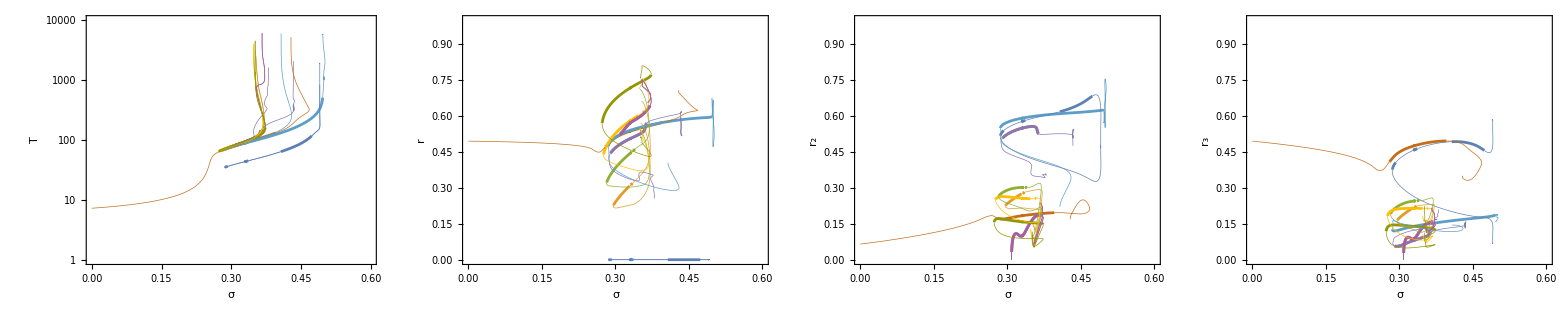

```mathematica
stable={};
unstable={};
Do[
branch=Catenate[{Reverse[DeleteCases[Import["auto/rel/small/"<>ToString[i]<>"rv.dat"],{}]],DeleteCases[Import["auto/rel/small/"<>ToString[i]<>"fw.dat"],{}]}];
stables={};
unstables={};
part={};
stab=0;
Do[If[stab==0,If[branch[[i,7]]<4*M-2 , AppendTo[part,branch[[i]]];,stab=1;AppendTo[unstables,part];part={branch[[i]]};], If[branch[[i,7]]<4*M-2,stab=0;AppendTo[stables,part];part={branch[[i]]};,AppendTo[part,branch[[i]]];];];,{i,1,Length[branch]}];
If[stab==0,AppendTo[unstables,part],AppendTo[stables,part]];AppendTo[stable,stables];AppendTo[unstable,unstables];,{i,1,10}];

Grid[{{Show[Show[Table[ListLogPlot[stable[[i,All,All,{1,3}]],PlotRange->{{0,0.6},{1,10^4}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,T},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[i]]]],{i,1,10}]],Show[Table[ListLogPlot[unstable[[i,All,All,{1,3}]],PlotRange->{{0,0.6},{1,10^4}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,T},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5],ColorData[97,"ColorList"][[i]]]],{i,{1,2,3,5,6,7,8,9,10}}]]],Show[Show[Table[ListPlot[stable[[i,All,All,{1,4}]],PlotRange->{{0,0.6},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[i]]]],{i,1,10}]],Show[Table[ListPlot[unstable[[i,All,All,{1,4}]],PlotRange->{{0,0.6},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5],ColorData[97,"ColorList"][[i]]]],{i,{1,2,3,5,6,7,8,9,10}}]]],Show[Show[Table[ListPlot[stable[[i,All,All,{1,5}]],PlotRange->{{0,0.6},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,Subscript[r,2]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[i]]]],{i,1,10}]],Show[Table[ListPlot[unstable[[i,All,All,{1,5}]],PlotRange->{{0,0.6},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,Subscript[r,2]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5],ColorData[97,"ColorList"][[i]]]],{i,{1,2,3,5,6,7,8,9,10}}]]],Show[Show[Table[ListPlot[stable[[i,All,All,{1,6}]],PlotRange->{{0,0.6},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,Subscript[r,3]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[i]]]],{i,1,10}]],Show[Table[ListPlot[unstable[[i,All,All,{1,6}]],PlotRange->{{0,0.6},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,Subscript[r,3]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5],ColorData[97,"ColorList"][[i]]]],{i,{1,2,3,5,6,7,8,9,10}}]]]}}]
```

### AUTO steady solutions

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{η→-2.36793},{η→-1.49156}}

{1:0.809017,2:0.309017,3:-0.309017,4:-0.809017,5:-1.0,6:-0.809017,7:-0.309017,8:0.309017,9:0.809017,10:0.587785,11:0.951057,12:0.951057,13:0.587785,14:0.0,15:-0.587785,16:-0.951057,17:-0.951057,18:-0.587785,19:-0.715353,20:-0.16801,21:0.443507,22:0.88562,23:0.989455,24:0.715353,25:0.16801,26:-0.443507,27:-0.88562,28:-0.989455,29:-0.698763,30:-0.985785,31:-0.896271,32:-0.464411,33:0.144838,34:0.698763,35:0.985785,36:0.896271,37:0.464411,38:-0.144838}

{-0.698763 β-0.985785 σ+ω/2,-0.698763 β-0.985785 σ+ω/2,-0.698763 β-0.985785 σ+ω/2,-0.698763 β-0.985785 σ+ω/2,-0.698763 β-0.985785 σ+ω/2,-0.698763 β-0.985785 σ+ω/2,-0.698763 β-0.985785 σ+ω/2,-0.698763 β-0.985785 σ+ω/2,-0.698763 β-0.985785 σ+ω/2,-0.698763 β-0.985785 σ+ω/2}

{0.698763 β+0.985785 σ-ω/2,0.698763 β+0.985785 σ-ω/2,0.698763 β+0.985785 σ-ω/2,0.698763 β+0.985785 σ-ω/2,0.698763 β+0.985785 σ-ω/2,0.698763 β+0.985785 σ-ω/2,0.698763 β+0.985785 σ-ω/2,0.698763 β+0.985785 σ-ω/2,0.698763 β+0.985785 σ-ω/2,0.698763 β+0.985785 σ-ω/2}

2.22045×10^-17

2.48253×10^-17

0.377258

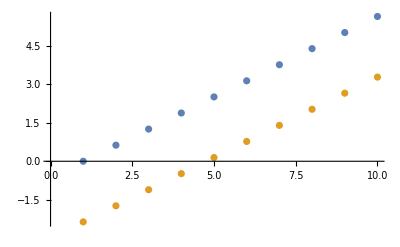

{1:0.809017,2:0.309017,3:-0.309017,4:-0.809017,5:-1.0,6:-0.809017,7:-0.309017,8:0.309017,9:0.809017,10:0.587785,11:0.951057,12:0.951057,13:0.587785,14:0.0,15:-0.587785,16:-0.951057,17:-0.951057,18:-0.587785,19:0.0791545,20:0.649978,21:0.972533,22:0.923612,23:0.521904,24:-0.0791545,25:-0.649978,26:-0.972533,27:-0.923612,28:-0.521904,29:-0.996862,30:-0.759953,31:-0.232767,32:0.383328,33:0.853004,34:0.996862,35:0.759953,36:0.232767,37:-0.383328,38:-0.853004}

{-0.996862 β-0.759953 σ+ω/2,-0.996862 β-0.759953 σ+ω/2,-0.996862 β-0.759953 σ+ω/2,-0.996862 β-0.759953 σ+ω/2,-0.996862 β-0.759953 σ+ω/2,-0.996862 β-0.759953 σ+ω/2,-0.996862 β-0.759953 σ+ω/2,-0.996862 β-0.759953 σ+ω/2,-0.996862 β-0.759953 σ+ω/2,-0.996862 β-0.759953 σ+ω/2}

{0.996862 β+0.759953 σ-ω/2,0.996862 β+0.759953 σ-ω/2,0.996862 β+0.759953 σ-ω/2,0.996862 β+0.759953 σ-ω/2,0.996862 β+0.759953 σ-ω/2,0.996862 β+0.759953 σ-ω/2,0.996862 β+0.759953 σ-ω/2,0.996862 β+0.759953 σ-ω/2,0.996862 β+0.759953 σ-ω/2,0.996862 β+0.759953 σ-ω/2}

6.66134×10^-17

4.96507×10^-17

0.734559

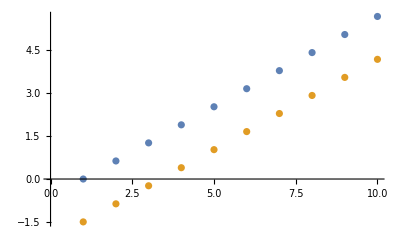

```mathematica
sols=Solve[0==1+2*0.25*Sin[η]+2*0.33*Sin[η+2*Pi/M],η]
thetas=Table[2*Pi/M*i,{i,1,M-1}];
phis=Table[η+2*Pi/M*i,{i,0,M-1}]/.sols[[1]];
u=Catenate[N[{Cos[thetas],Sin[thetas],Cos[phis],Sin[phis]}]];
Table[ToString[i]<>":"<>TextString[u[[i]]],{i,1,4*M-2}]

theta=N[Join[{0},thetas]];
Table[ω/2+β*Sin[phis[[i]]-theta[[i]]]+σ*Sin[phis[[Mod[i+1-1,M]+1]]-theta[[i]]],{i,1,M}]
Table[-ω/2+β*Sin[theta[[i]]-phis[[i]]]+σ*Sin[theta[[Mod[i-1-1,M]+1]]-phis[[i]]],{i,1,M}]
Abs[Total[Exp[I*theta]+Exp[I*phis]]/(2*M)]
Abs[Total[Exp[I*(theta+2*Pi*Range[M]/M)]+Exp[I*(phis+2*Pi*Range[M]/M)]]/(2*M)]
Abs[Total[Exp[I*(theta-2*Pi*Range[M]/M)]+Exp[I*(phis-2*Pi*Range[M]/M)]]/(2*M)]
ListPlot[{theta,phis}]

thetas=Table[2*Pi/M*i,{i,1,M-1}];
phis=Table[η+2*Pi/M*i,{i,0,M-1}]/.sols[[2]];
u=Catenate[N[{Cos[thetas],Sin[thetas],Cos[phis],Sin[phis]}]];
Table[ToString[i]<>":"<>TextString[u[[i]]],{i,1,4*M-2}]

theta=N[Join[{0},thetas]];
Table[ω/2+β*Sin[phis[[i]]-theta[[i]]]+σ*Sin[phis[[Mod[i+1-1,M]+1]]-theta[[i]]],{i,1,M}]
Table[-ω/2+β*Sin[theta[[i]]-phis[[i]]]+σ*Sin[theta[[Mod[i-1-1,M]+1]]-phis[[i]]],{i,1,M}]
Abs[Total[Exp[I*theta]+Exp[I*phis]]/(2*M)]
Abs[Total[Exp[I*(theta+2*Pi*Range[M]/M)]+Exp[I*(phis+2*Pi*Range[M]/M)]]/(2*M)]
Abs[Total[Exp[I*(theta-2*Pi*Range[M]/M)]+Exp[I*(phis-2*Pi*Range[M]/M)]]/(2*M)]
ListPlot[{theta,phis}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{η→-1.65003},{η→-0.773667}}

{1:0.809017,2:0.309017,3:-0.309017,4:-0.809017,5:-1.0,6:-0.809017,7:-0.309017,8:0.309017,9:0.809017,10:-0.587785,11:-0.951057,12:-0.951057,13:-0.587785,14:0.0,15:0.587785,16:0.951057,17:0.951057,18:0.587785,19:-0.0791545,20:-0.649978,21:-0.972533,22:-0.923612,23:-0.521904,24:0.0791545,25:0.649978,26:0.972533,27:0.923612,28:0.521904,29:-0.996862,30:-0.759953,31:-0.232767,32:0.383328,33:0.853004,34:0.996862,35:0.759953,36:0.232767,37:-0.383328,38:-0.853004}

{-0.996862 β-0.759953 σ+ω/2,-0.996862 β-0.759953 σ+ω/2,-0.996862 β-0.759953 σ+ω/2,-0.996862 β-0.759953 σ+ω/2,-0.996862 β-0.759953 σ+ω/2,-0.996862 β-0.759953 σ+ω/2,-0.996862 β-0.759953 σ+ω/2,-0.996862 β-0.759953 σ+ω/2,-0.996862 β-0.759953 σ+ω/2,-0.996862 β-0.759953 σ+ω/2}

{0.996862 β+0.759953 σ-ω/2,0.996862 β+0.759953 σ-ω/2,0.996862 β+0.759953 σ-ω/2,0.996862 β+0.759953 σ-ω/2,0.996862 β+0.759953 σ-ω/2,0.996862 β+0.759953 σ-ω/2,0.996862 β+0.759953 σ-ω/2,0.996862 β+0.759953 σ-ω/2,0.996862 β+0.759953 σ-ω/2,0.996862 β+0.759953 σ-ω/2}

4.44089×10^-17

0.678545

1.57009×10^-17

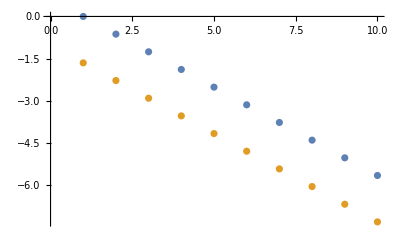

{1:0.809017,2:0.309017,3:-0.309017,4:-0.809017,5:-1.0,6:-0.809017,7:-0.309017,8:0.309017,9:0.809017,10:-0.587785,11:-0.951057,12:-0.951057,13:-0.587785,14:0.0,15:0.587785,16:0.951057,17:0.951057,18:0.587785,19:0.715353,20:0.16801,21:-0.443507,22:-0.88562,23:-0.989455,24:-0.715353,25:-0.16801,26:0.443507,27:0.88562,28:0.989455,29:-0.698763,30:-0.985785,31:-0.896271,32:-0.464411,33:0.144838,34:0.698763,35:0.985785,36:0.896271,37:0.464411,38:-0.144838}

{-0.698763 β-0.985785 σ+ω/2,-0.698763 β-0.985785 σ+ω/2,-0.698763 β-0.985785 σ+ω/2,-0.698763 β-0.985785 σ+ω/2,-0.698763 β-0.985785 σ+ω/2,-0.698763 β-0.985785 σ+ω/2,-0.698763 β-0.985785 σ+ω/2,-0.698763 β-0.985785 σ+ω/2,-0.698763 β-0.985785 σ+ω/2,-0.698763 β-0.985785 σ+ω/2}

{0.698763 β+0.985785 σ-ω/2,0.698763 β+0.985785 σ-ω/2,0.698763 β+0.985785 σ-ω/2,0.698763 β+0.985785 σ-ω/2,0.698763 β+0.985785 σ-ω/2,0.698763 β+0.985785 σ-ω/2,0.698763 β+0.985785 σ-ω/2,0.698763 β+0.985785 σ-ω/2,0.698763 β+0.985785 σ-ω/2,0.698763 β+0.985785 σ-ω/2}

4.96507×10^-17

0.926108

4.00297×10^-17

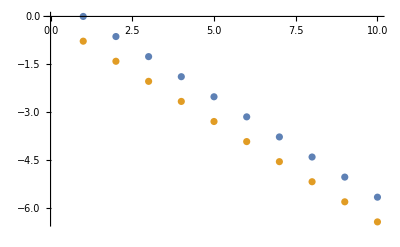

```mathematica
sols=Solve[0==1+2*0.25*Sin[η]+2*0.33*Sin[η-2*Pi/M],η]
thetas=Table[-2*Pi/M*i,{i,1,M-1}];
phis=Table[η-2*Pi/M*i,{i,0,M-1}]/.sols[[1]];
u=Catenate[N[{Cos[thetas],Sin[thetas],Cos[phis],Sin[phis]}]];
Table[ToString[i]<>":"<>TextString[u[[i]]],{i,1,4*M-2}]

theta=N[Join[{0},thetas]];
Table[ω/2+β*Sin[phis[[i]]-theta[[i]]]+σ*Sin[phis[[Mod[i+1-1,M]+1]]-theta[[i]]],{i,1,M}]
Table[-ω/2+β*Sin[theta[[i]]-phis[[i]]]+σ*Sin[theta[[Mod[i-1-1,M]+1]]-phis[[i]]],{i,1,M}]
Abs[Total[Exp[I*theta]+Exp[I*phis]]/(2*M)]
Abs[Total[Exp[I*(theta+2*Pi*Range[M]/M)]+Exp[I*(phis+2*Pi*Range[M]/M)]]/(2*M)]
Abs[Total[Exp[I*(theta-2*Pi*Range[M]/M)]+Exp[I*(phis-2*Pi*Range[M]/M)]]/(2*M)]
ListPlot[{theta,phis}]

thetas=Table[-2*Pi/M*i,{i,1,M-1}];
phis=Table[η-2*Pi/M*i,{i,0,M-1}]/.sols[[2]];
u=Catenate[N[{Cos[thetas],Sin[thetas],Cos[phis],Sin[phis]}]];
Table[ToString[i]<>":"<>TextString[u[[i]]],{i,1,4*M-2}]

theta=N[Join[{0},thetas]];
Table[ω/2+β*Sin[phis[[i]]-theta[[i]]]+σ*Sin[phis[[Mod[i+1-1,M]+1]]-theta[[i]]],{i,1,M}]
Table[-ω/2+β*Sin[theta[[i]]-phis[[i]]]+σ*Sin[theta[[Mod[i-1-1,M]+1]]-phis[[i]]],{i,1,M}]
Abs[Total[Exp[I*theta]+Exp[I*phis]]/(2*M)]
Abs[Total[Exp[I*(theta+2*Pi*Range[M]/M)]+Exp[I*(phis+2*Pi*Range[M]/M)]]/(2*M)]
Abs[Total[Exp[I*(theta-2*Pi*Range[M]/M)]+Exp[I*(phis-2*Pi*Range[M]/M)]]/(2*M)]
ListPlot[{theta,phis}]
```

#### Cluster twisted steady states

```mathematica
η=0;
σ=0.33;
β=0.25;
ω=1;
θ1=0;
AbsoluteTiming[vals=Mod[{θ2,ϕ1,ϕ2},2*Pi]/.DeleteCases[Table[SeedRandom[seed];Quiet[Check[FindRoot[{0==ω/2+β*Sin[ϕ1]+σ*Sin[ϕ2+η],0==-ω/2+β*Sin[-ϕ1]+σ*Sin[θ2-ϕ1-η],0==ω/2+β*Sin[ϕ2-θ2]+σ*Sin[ϕ1-θ2+η]},{{θ2,2*Pi*RandomReal[]},{ϕ1,2*Pi*RandomReal[]},{ϕ2,2*Pi*RandomReal[]}}],{}]],{seed,1,10000}],{}];]
dtheta=0.01;
{bins,array}=HistogramList[vals[[All,1;;3]],{{-Pi*dtheta+2*Pi*dtheta*(Range[1.0/dtheta]-1)},{-Pi*dtheta+2*Pi*dtheta*(Range[1.0/dtheta]-1)},{-Pi*dtheta+2*Pi*dtheta*(Range[1.0/dtheta]-1)}}];
uniq=Table[{i,j,k}=case;
First@Cases[vals,u_/;u[[1]]>=bins[[1,i]]&&u[[1]]<=bins[[1,i+1]]&&u[[2]]>=bins[[2,j]]&&u[[2]]<=bins[[2,j+1]]&&u[[3]]>=bins[[3,k]]&&u[[3]]<=bins[[3,k+1]]],{case,(First/@ArrayRules[array])[[1;;-2]]}];
{Length[uniq],Length[vals]}
SortBy[{#[[1]],#[[2]],#[[3]]}&/@uniq,{#[[1]],#[[2]],#[[3]]}&]
```

{7.97856,Null}

{158,9890}

{{-0.0307549,5.22615,4.16787},{-0.01379,4.17312,5.23786},{-2.07168×10^-17,5.24385,5.24385},{2.18411×10^-16,4.18093,4.18093},{0.00296324,5.24553,4.18221},{0.00413711,4.18329,5.24563},{0.0268497,5.25897,4.19265},{0.0277364,4.19687,5.25564},{0.0628256,5.27877,4.20883},{0.0695028,4.22149,5.27279},{0.0965555,5.29684,4.22449},{0.101187,4.24065,5.28531},{0.126452,5.31246,4.23877},{0.132737,4.26016,5.29736},{0.1419,5.32038,4.2463},{0.164472,4.28022,5.30903},{0.184402,4.29305,5.31613},{0.210661,5.35439,4.28105},{0.211777,4.31095,5.3256},{0.2386,5.36761,4.29577},{0.246394,4.33409,5.33708},{0.263814,5.37925,4.30935},{0.292654,4.36589,5.35154},{0.294723,4.36734,5.35217},{0.309637,5.39964,4.33478},{0.351901,4.40817,5.36851},{0.355331,5.41896,4.36115},{0.370543,5.42516,4.37016},{0.37194,4.42288,5.37384},{0.402412,4.44567,5.38152},{0.407359,5.43968,4.39246},{0.416374,4.45629,5.38486},{0.463366,5.46033,4.42781},{0.464087,4.49344,5.39542},{0.493527,4.51707,5.40123},{0.498304,5.47229,4.4508},{0.536594,5.4845,4.47687},{0.564336,5.49273,4.49639},{0.576901,4.58721,5.41446},{0.584347,5.49832,4.5108},{0.602597,4.60989,5.41748},{0.617709,5.50696,4.53553},{0.620739,4.62624,5.41928},{0.654807,5.51548,4.5641},{0.663701,4.66613,5.42235},{0.67315,5.51923,4.57869},{0.699155,4.70042,5.42351},{0.720898,5.52742,4.61825},{0.731553,4.73298,5.42335},{0.74683,5.5308,4.64081},{0.761273,4.764,5.42205},{0.787309,5.53434,4.67775},{0.789946,4.79511,5.41962},{0.838613,4.851,5.41239},{0.846708,5.5349,4.73659},{0.851991,4.86716,5.40961},{0.85797,5.53425,4.7485},{0.862688,4.88037,5.4071},{0.90847,4.94018,5.39307},{0.929414,5.52256,4.83163},{0.943344,4.99028,5.37784},{0.948907,4.99874,5.37494},{0.966497,5.50927,4.88201},{0.970739,5.03347,5.36204},{0.977733,5.50379,4.89872},{0.984633,5.0571,5.35231},{0.992357,5.07086,5.34628},{0.99557,5.49325,4.9271},{1.02697,5.14036,5.31138},{1.03024,5.463,4.99202},{1.03432,5.45814,5.00095},{1.03626,5.1623,5.29874},{1.0397,5.17097,5.29351},{1.04313,5.44613,5.02177},{1.04829,5.19434,5.27873},{1.05107,5.43292,5.04294},{1.05952,5.41486,5.06943},{1.06316,5.24486,5.24308},{1.0689,5.27252,5.22116},{1.07109,5.37261,5.12325},{1.07364,5.31177,5.18664},{1.0739,5.31642,5.18226},{5.20969,4.11513,4.23615},{5.2109,4.06043,4.29207},{5.21224,4.05129,4.30255},{5.21504,4.15648,4.20015},{5.22045,4.18167,4.18037},{5.2216,4.01533,4.34787},{5.23089,3.99417,4.37832},{5.23697,4.23637,4.1422},{5.23929,3.97981,4.40107},{5.23993,4.24447,4.13705},{5.25116,4.27272,4.12003},{5.25136,3.96362,4.42933},{5.25271,3.96205,4.43225},{5.2644,4.30233,4.10367},{5.27264,4.3193,4.09494},{5.29241,3.92845,4.50555},{5.29761,3.92531,4.51389},{5.30727,4.38266,4.0662},{5.31436,3.91658,4.53938},{5.31975,4.40322,4.05812},{5.33473,4.42674,4.04959},{5.35558,3.90172,4.59546},{5.35856,4.46196,4.03819},{5.37808,4.4892,4.03047},{5.38339,4.49639,4.02859},{5.39464,3.89376,4.64248},{5.43061,3.89019,4.68202},{5.43236,4.55904,4.01491},{5.45696,4.58841,4.01014},{5.46632,3.88939,4.71852},{5.49443,4.63099,4.00504},{5.49554,3.89042,4.74672},{5.49826,4.63521,4.00465},{5.53499,3.89382,4.78276},{5.55636,4.69662,4.00133},{5.56224,3.89735,4.80649},{5.58827,4.72853,4.00134},{5.60959,3.90546,4.84572},{5.61626,4.75559,4.00227},{5.6314,3.90995,4.86305},{5.65023,4.78737,4.00445},{5.6775,4.81212,4.00697},{5.67899,3.92121,4.89937},{5.68664,3.9232,4.90504},{5.68858,4.822,4.00818},{5.71002,3.92955,4.92207},{5.74714,4.87256,4.01617},{5.74806,3.94073,4.94892},{5.75266,3.94215,4.9521},{5.75648,4.88039,4.01768},{5.8134,3.96219,4.9928},{5.81735,4.92995,4.02899},{5.81963,3.96438,4.99684},{5.85469,4.95918,4.0371},{5.87478,3.9847,5.03168},{5.90127,4.99449,4.04837},{5.90583,3.99687,5.05055},{5.91534,5.00492,4.05201},{5.92317,5.01068,4.05408},{5.93703,4.00961,5.06901},{5.97423,5.04744,4.06839},{5.99395,5.06127,4.07427},{6.00026,4.03691,5.10494},{6.01437,4.04326,5.11271},{6.03233,4.05147,5.12245},{6.04275,5.09471,4.08963},{6.0562,4.06262,5.13517},{6.06579,5.11011,4.09727},{6.08468,5.12255,4.10372},{6.09647,4.082,5.15606},{6.11841,5.14437,4.11564},{6.13325,5.1538,4.12104},{6.14897,4.10833,5.18223},{6.15186,4.10981,5.18364},{6.1843,5.18554,4.14036},{6.1845,4.12681,5.19928}}

```mathematica
Monitor[Do[{θ2,ϕ1,ϕ2}=uniq[[i]];
thetas=Riffle[Table[θ2+η*i,{i,1,M-1,2}],Table[0+η*i,{i,2,M-1,2}]];
phis=Riffle[Table[ϕ1+η*i,{i,0,M-1,2}],Table[ϕ2+η*i,{i,1,M-1,2}]];
u=Catenate[N[{Cos[thetas],Sin[thetas],Cos[phis],Sin[phis]}]];
lines=StringJoin[{Import["auto/rel/small/clusters/c.cluster"],"\nU="<>ToString[Table[ToString[i]<>":"<>TextString[u[[i]]],{i,1,4*M-2}]]}];
file=OpenWrite["auto/rel/small/clusters/c.cluster"<>ToString[i]];
WriteLine[file,lines];
Close[file];,{i,1,Length[uniq]}],i]
```

```mathematica
η=2*Pi/M;
σ=0.33;
β=0.25;
ω=1;
θ1=0;
AbsoluteTiming[vals=Mod[{θ2,ϕ1,ϕ2},2*Pi]/.DeleteCases[Table[SeedRandom[seed];Quiet[Check[FindRoot[{0==ω/2+β*Sin[ϕ1]+σ*Sin[ϕ2+η],0==-ω/2+β*Sin[-ϕ1]+σ*Sin[θ2-ϕ1-η],0==ω/2+β*Sin[ϕ2-θ2]+σ*Sin[ϕ1-θ2+η]},{{θ2,2*Pi*RandomReal[]},{ϕ1,2*Pi*RandomReal[]},{ϕ2,2*Pi*RandomReal[]}}],{}]],{seed,1,10000}],{}];]
dtheta=0.01;
{bins,array}=HistogramList[vals[[All,1;;3]],{{-Pi*dtheta+2*Pi*dtheta*(Range[1.0/dtheta]-1)},{-Pi*dtheta+2*Pi*dtheta*(Range[1.0/dtheta]-1)},{-Pi*dtheta+2*Pi*dtheta*(Range[1.0/dtheta]-1)}}];
uniq=Table[{i,j,k}=case;
First@Cases[vals,u_/;u[[1]]>=bins[[1,i]]&&u[[1]]<=bins[[1,i+1]]&&u[[2]]>=bins[[2,j]]&&u[[2]]<=bins[[2,j+1]]&&u[[3]]>=bins[[3,k]]&&u[[3]]<=bins[[3,k+1]]],{case,(First/@ArrayRules[array])[[1;;-2]]}];
{Length[uniq],Length[vals]}
uniq
```

{9.01866,Null}

{6,9329}

{{-6.09847×10^-16,3.91526,3.91526},{6.92834×10^-16,4.79163,4.79163},{0.370635,5.08302,4.71239},{0.445814,4.08407,4.52988},{5.83737,4.08407,3.63826},{5.91255,4.34175,4.71239}}

```mathematica
Monitor[Do[{θ2,ϕ1,ϕ2}=uniq[[i]];
thetas=Riffle[Table[θ2+η*i,{i,1,M-1,2}],Table[0+η*i,{i,2,M-1,2}]];
phis=Riffle[Table[ϕ1+η*i,{i,0,M-1,2}],Table[ϕ2+η*i,{i,1,M-1,2}]];
u=Catenate[N[{Cos[thetas],Sin[thetas],Cos[phis],Sin[phis]}]];
lines=StringJoin[{Import["auto/rel/small/clusters1/c.cluster"],"\nU="<>ToString[Table[ToString[i]<>":"<>TextString[u[[i]]],{i,1,4*M-2}]]}];
file=OpenWrite["auto/rel/small/clusters1/c.cluster"<>ToString[i]];
WriteLine[file,lines];
Close[file];,{i,1,Length[uniq]}],i]
```

```mathematica
η=-2*Pi/M;
σ=0.33;
β=0.25;
ω=1;
θ1=0;
AbsoluteTiming[vals=Mod[{θ2,ϕ1,ϕ2},2*Pi]/.DeleteCases[Table[SeedRandom[seed];Quiet[Check[FindRoot[{0==ω/2+β*Sin[ϕ1]+σ*Sin[ϕ2+η],0==-ω/2+β*Sin[-ϕ1]+σ*Sin[θ2-ϕ1-η],0==ω/2+β*Sin[ϕ2-θ2]+σ*Sin[ϕ1-θ2+η]},{{θ2,2*Pi*RandomReal[]},{ϕ1,2*Pi*RandomReal[]},{ϕ2,2*Pi*RandomReal[]}}],{}]],{seed,1,10000}],{}];]
dtheta=0.01;
{bins,array}=HistogramList[vals[[All,1;;3]],{{-Pi*dtheta+2*Pi*dtheta*(Range[1.0/dtheta]-1)},{-Pi*dtheta+2*Pi*dtheta*(Range[1.0/dtheta]-1)},{-Pi*dtheta+2*Pi*dtheta*(Range[1.0/dtheta]-1)}}];
uniq=Table[{i,j,k}=case;
First@Cases[vals,u_/;u[[1]]>=bins[[1,i]]&&u[[1]]<=bins[[1,i+1]]&&u[[2]]>=bins[[2,j]]&&u[[2]]<=bins[[2,j+1]]&&u[[3]]>=bins[[3,k]]&&u[[3]]<=bins[[3,k+1]]],{case,(First/@ArrayRules[array])[[1;;-2]]}];
{Length[uniq],Length[vals]}
uniq
```

{9.13667,Null}

{6,9365}

{{-2.42599×10^-16,4.63315,4.63315},{9.62523×10^-17,5.50952,5.50952},{0.370635,5.08302,4.71239},{0.445814,5.34071,5.78652},{5.83737,5.34071,4.89489},{5.91255,4.34175,4.71239}}

```mathematica
Monitor[Do[{θ2,ϕ1,ϕ2}=uniq[[i]];
thetas=Riffle[Table[θ2+η*i,{i,1,M-1,2}],Table[0+η*i,{i,2,M-1,2}]];
phis=Riffle[Table[ϕ1+η*i,{i,0,M-1,2}],Table[ϕ2+η*i,{i,1,M-1,2}]];
u=Catenate[N[{Cos[thetas],Sin[thetas],Cos[phis],Sin[phis]}]];
lines=StringJoin[{Import["auto/rel/small/clusters2/c.cluster"],"\nU="<>ToString[Table[ToString[i]<>":"<>TextString[u[[i]]],{i,1,4*M-2}]]}];
file=OpenWrite["auto/rel/small/clusters2/c.cluster"<>ToString[i]];
WriteLine[file,lines];
Close[file];,{i,1,Length[uniq]}],i]
```

#### Plots of sweeps

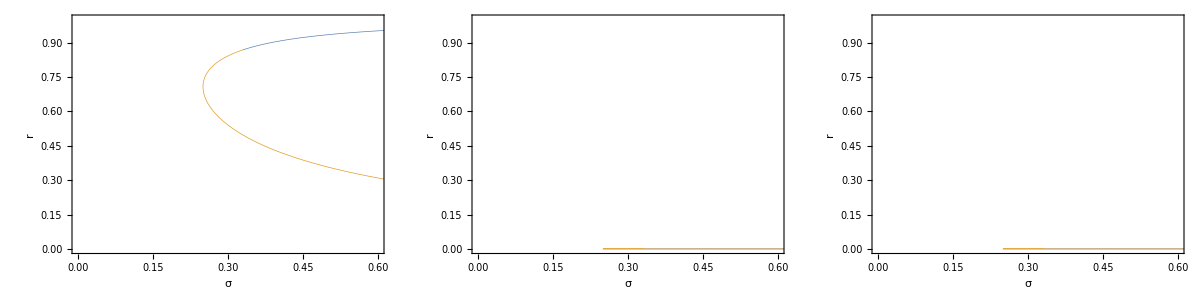

```mathematica
steady=Join[{#[[1;;Position[#,{}][[1,1]]-1]]},Table[#[[Position[#,{}][[i,1]]+1;;Position[#,{}][[i+1,1]]-1]],{i,1,Length[Position[#,{}]]-1}]]&@Import["auto/rel/small/steady/steady.dat"];
Grid[{{ListPlot[steady[[All,All,{1,4}]],PlotRange->{{0,0.6},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]],ListPlot[steady[[All,All,{1,5}]],PlotRange->{{0,0.6},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]],ListPlot[steady[[All,All,{1,6}]],PlotRange->{{0,0.6},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]]}}]
```

```mathematica
twists1=Join[{#[[1;;Position[#,{}][[1,1]]-1]]},Table[#[[Position[#,{}][[i,1]]+1;;Position[#,{}][[i+1,1]]-1]],{i,1,Length[Position[#,{}]]-1}]]&@Import["auto/rel/small/twist1/twists.dat"];
Grid[{{rasterizeBackground[ListPlot[twists1[[All,All,{1,4}]],PlotRange->{{0,0.6},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]]],rasterizeBackground[ListPlot[twists1[[All,All,{1,5}]],PlotRange->{{0,0.6},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]]],rasterizeBackground[ListPlot[twists1[[All,All,{1,6}]],PlotRange->{{0,0.6},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]]]}}]
```

-Graphics- | -Graphics- | -Graphics-

```mathematica
twists2=Join[{#[[1;;Position[#,{}][[1,1]]-1]]},Table[#[[Position[#,{}][[i,1]]+1;;Position[#,{}][[i+1,1]]-1]],{i,1,Length[Position[#,{}]]-1}]]&@Import["auto/rel/small/twist2/twists.dat"];
Grid[{{rasterizeBackground[ListPlot[twists2[[All,All,{1,4}]],PlotRange->{{0,0.6},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]]],rasterizeBackground[ListPlot[twists2[[All,All,{1,5}]],PlotRange->{{0,0.6},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]]],rasterizeBackground[ListPlot[twists2[[All,All,{1,6}]],PlotRange->{{0,0.6},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]]]}}]
```

-Graphics- | -Graphics- | -Graphics-

```mathematica
clusters1=Join[{#[[1;;Position[#,{}][[1,1]]-1]]},Table[#[[Position[#,{}][[i,1]]+1;;Position[#,{}][[i+1,1]]-1]],{i,1,Length[Position[#,{}]]-1}]]&@Import["auto/rel/small/clusters1/clusters.dat"];
Grid[{{rasterizeBackground[ListPlot[clusters1[[All,All,{1,4}]],PlotRange->{{0,0.6},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]]],rasterizeBackground[ListPlot[clusters1[[All,All,{1,5}]],PlotRange->{{0,0.6},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]]],rasterizeBackground[ListPlot[clusters1[[All,All,{1,6}]],PlotRange->{{0,0.6},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]]]}}]
```

-Graphics- | -Graphics- | -Graphics-

```mathematica
clusters2=Join[{#[[1;;Position[#,{}][[1,1]]-1]]},Table[#[[Position[#,{}][[i,1]]+1;;Position[#,{}][[i+1,1]]-1]],{i,1,Length[Position[#,{}]]-1}]]&@Import["auto/rel/small/clusters2/clusters.dat"];
Grid[{{rasterizeBackground[ListPlot[clusters2[[All,All,{1,4}]],PlotRange->{{0,0.6},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]]],rasterizeBackground[ListPlot[clusters2[[All,All,{1,5}]],PlotRange->{{0,0.6},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]]],rasterizeBackground[ListPlot[clusters2[[All,All,{1,6}]],PlotRange->{{0,0.6},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]]]}}]
```

-Graphics- | -Graphics- | -Graphics-

```mathematica
all=Join[steady,twists1,twists2,clusters1,clusters2];
Grid[{{rasterizeBackground[ListPlot[all[[All,All,{1,4}]],PlotRange->{{0,0.6},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]]],rasterizeBackground[ListPlot[all[[All,All,{1,5}]],PlotRange->{{0,0.6},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]]],rasterizeBackground[ListPlot[all[[All,All,{1,6}]],PlotRange->{{0,0.6},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]]]}}]
```

-Graphics- | -Graphics- | -Graphics-

```mathematica
AbsoluteTiming[Monitor[branches=Table[Import["auto/rel/small/clusters/branches/"<>ToString[i]<>".dat"],{i,1,6099}];,i]]
```

{228.643,Null}

```mathematica
dist[branch1_,branch2_]:=Module[{min,max,c1,c2,f1,f2,x,range},
{min,max}={Max[{Min[branch1[[All,1]]],Min[branch2[[All,1]]]}],Min[{Max[branch1[[All,1]]],Max[branch2[[All,1]]]}]};
c1=Cases[DeleteDuplicatesBy[branch1,#[[1]]&],u_/;u[[1]]>=min&&u[[1]]<=max];
c2=Cases[DeleteDuplicatesBy[branch2,#[[1]]&],u_/;u[[1]]>=min&&u[[1]]<=max];
{min,max}={Max[{Min[c1[[All,1]]],Min[c2[[All,1]]]}],Min[{Max[c1[[All,1]]],Max[c2[[All,1]]]}]};
If[max>min&&Length[c1]>1&&Length[c2]>1,f1=Interpolation[c1[[All,{1,4}]],InterpolationOrder->1];
f2=Interpolation[c2[[All,{1,4}]],InterpolationOrder->1];
range=(max-min);
Sum[Abs[f1[x]-f2[x]],{x,min+range/100,max-range/100,range/100}]/range,Infinity]]
AbsoluteTiming[Monitor[distances=Flatten[Table[{i,j,dist[branches[[i]],branches[[j]]]},{i,1,1},{j,i+1,Length[branches]}],1];,{i,j}]]
Cases[distances,u_/;u[[1]]<1]
```

```mathematica
AbsoluteTiming[rasterizeBackground[ListPlot[branches[[All,All,{1,4}]],PlotRange->{{0,1},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]]]]
```

{2039.09,-Graphics-}